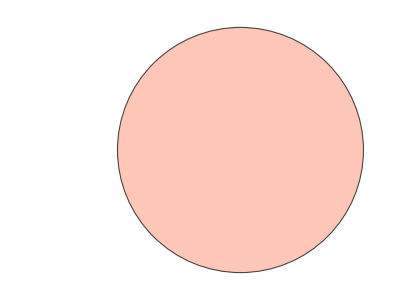
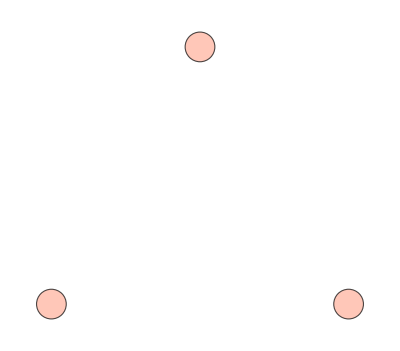
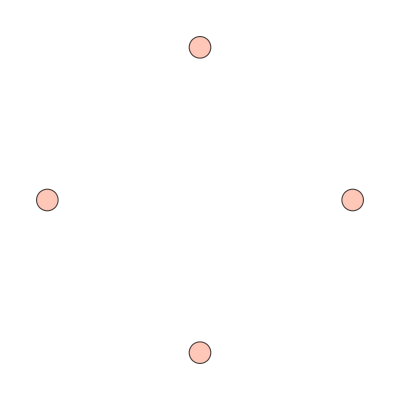
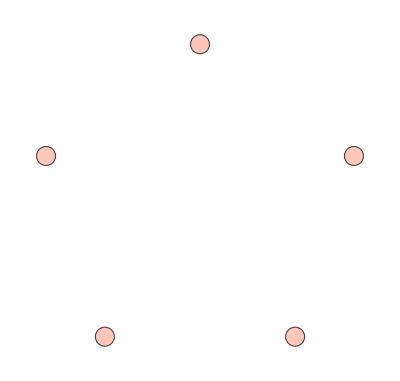
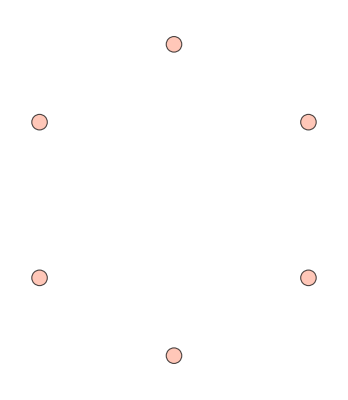
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[CycleGraph[i,EdgeStyle->White,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]],{i,1,6}]
```

```mathematica
Table[CompleteGraph[i,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]],{i,1,6}]
```

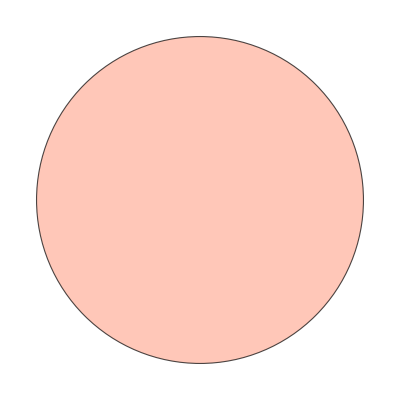
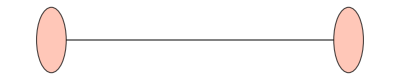
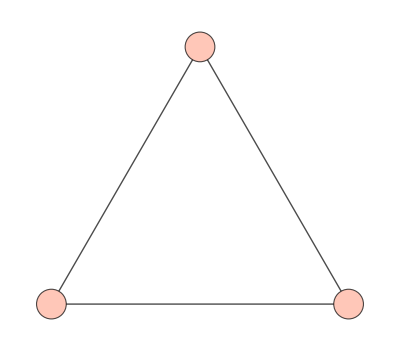
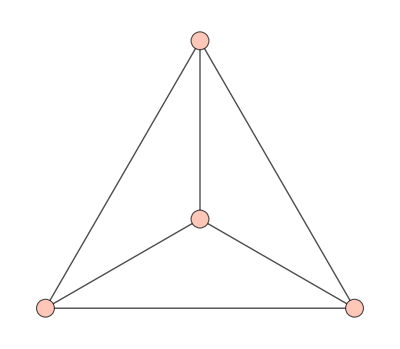
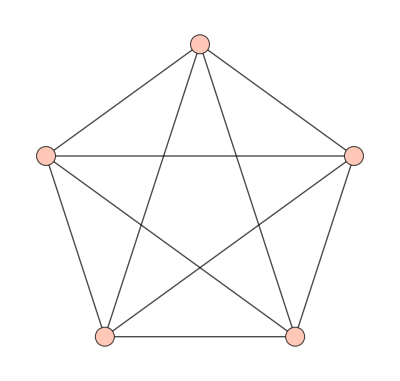
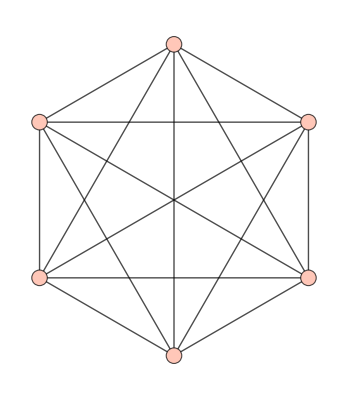

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
CycleGraph[1,VertexStyle->RGBColor[1,.78,.72]]
Table[CycleGraph[i,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]],{i,2,6}]
```

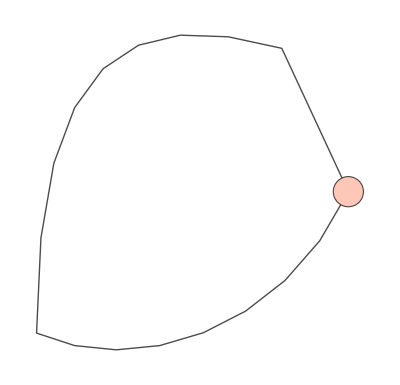

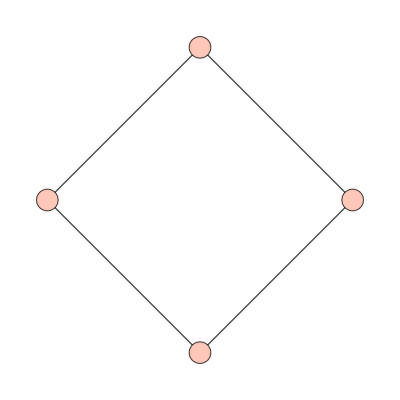
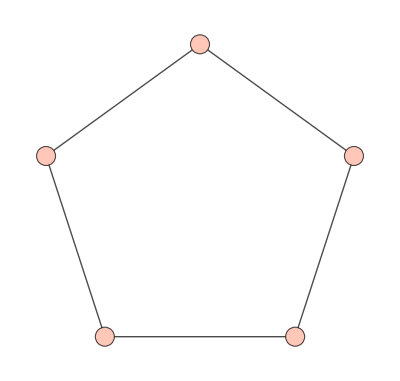
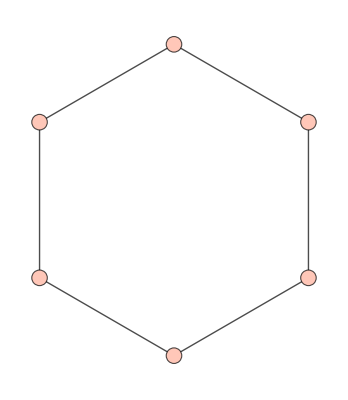
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Table[PathGraph[Table[k,{k,i}],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]],{i,1,6}]
```

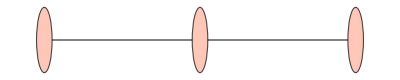
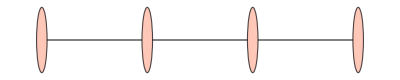
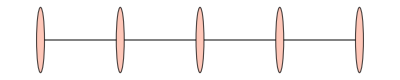
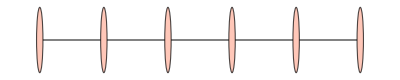
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

Set::write: Tag Inherited in Inherited[State] is Protected.

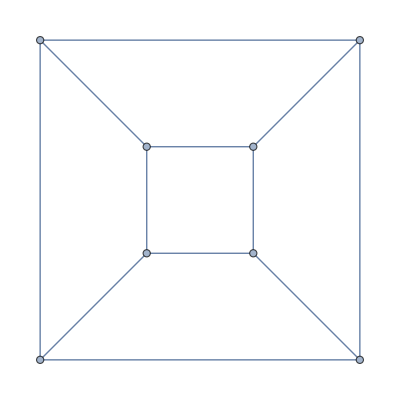

True

-Graphics-

-Graphics-

```mathematica
GraphData["CubicalGraph"]
BipartiteGraphQ[%]
Graph[-Graphics-]
Graph[-Graphics-]
```

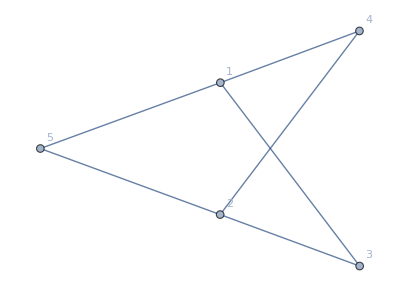
```mathematica
Graph[-Graphics-,VertexLabels->Automatic]
AdjacencyGraph[AdjacencyMatrix[-Graphics-],DirectedEdges->False,VertexLabels->Automatic]
BipartiteGraphQ[-Graphics-]
Graph[-Graphics-,VertexLabels->Automatic]
BipartiteGraphQ[CompleteGraph[{2,3}]]
```

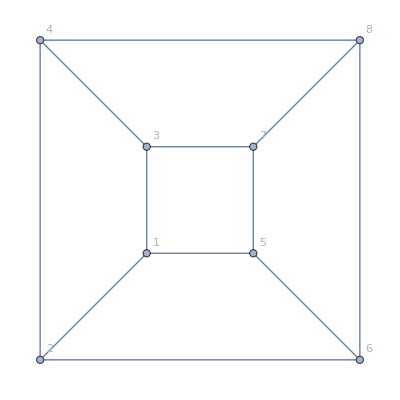

-Graphics-

True

-Graphics-

True

```mathematica
g=Graph[-Graphics-,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];
HighlightGraph[g,{4,1,7,6}]
(*g=Graph[AdjacencyGraph[AdjacencyMatrix[-Graphics-],DirectedEdges->False],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];*)
g=CompleteGraph[{2,3},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];
HighlightGraph[g,{1,2}]

g=StarGraph[6,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];
BipartiteGraphQ[%]
HighlightGraph[g,{1}]
g=CompleteGraph[{2,2},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];
BipartiteGraphQ[%]
HighlightGraph[g,{1,2}]
g=CompleteGraph[{2,4},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];
BipartiteGraphQ[%]
HighlightGraph[g,{1,2}]
g=CompleteGraph[{3,3},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]];
BipartiteGraphQ[%]
HighlightGraph[g,{1,2,3}]
```

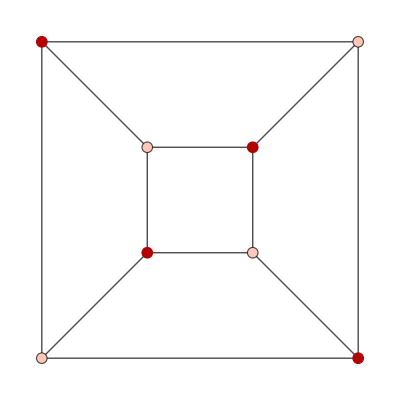

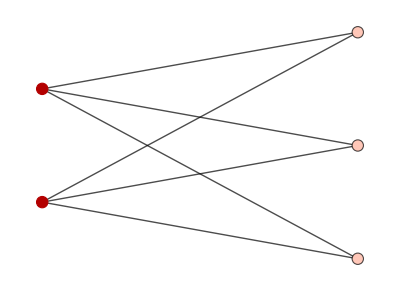

True

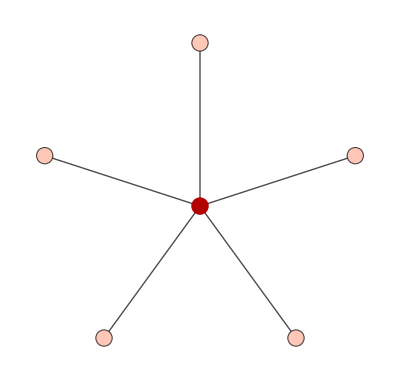

True

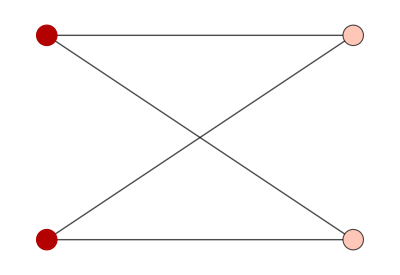

True

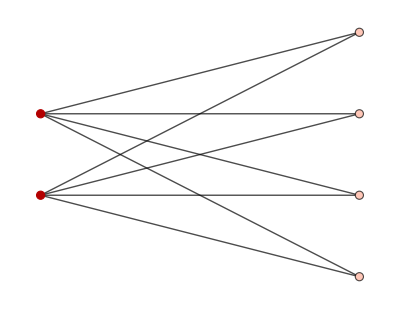

True

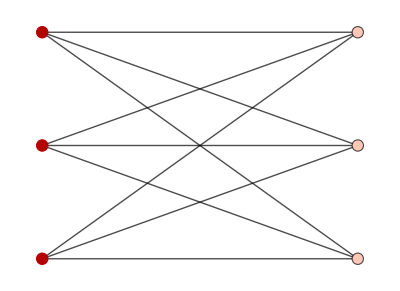

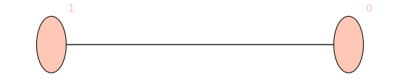
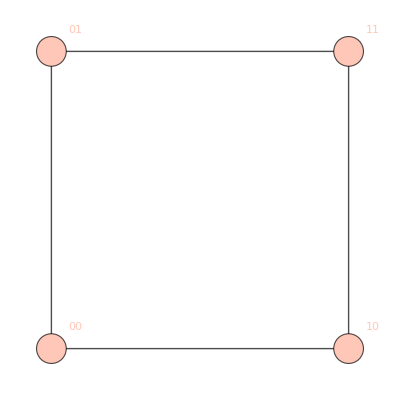
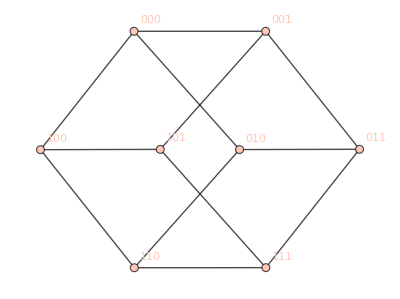
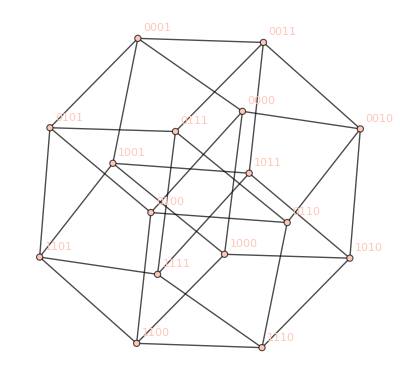

-Graphics-

```mathematica
este=Table[HypercubeGraph[i,VertexSize->Small,EdgeStyle->{Black},VertexStyle->RGBColor[1,.78,.72],VertexLabels->Table[k-> If[StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]<i,StringJoin[Table["0",i-StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]]]<>ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]],ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]],{k,0,2^i}]],{i,1,4}]
este[[1]]
```

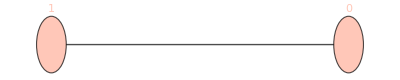
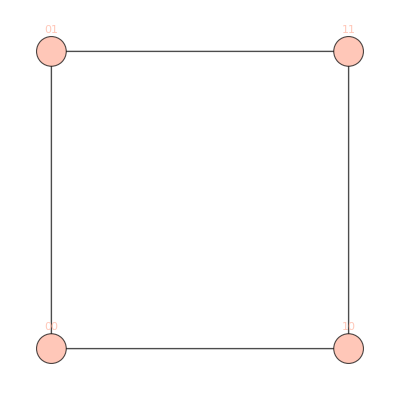
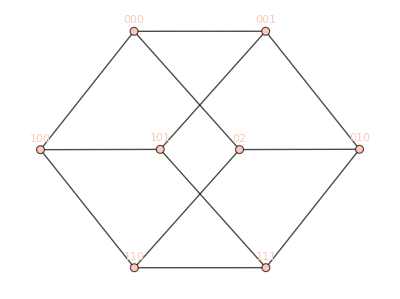
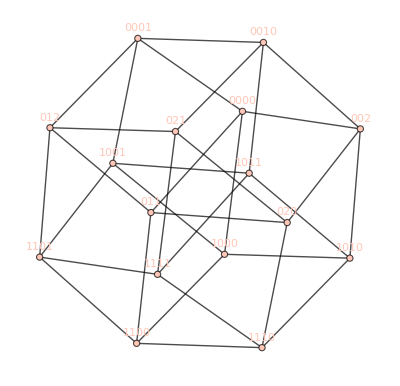

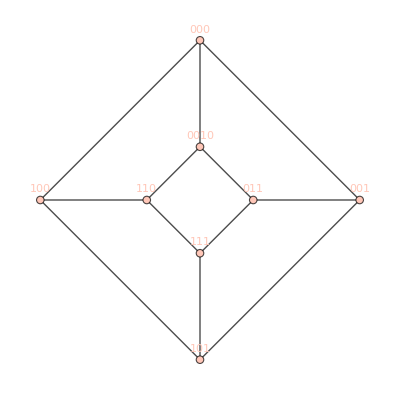

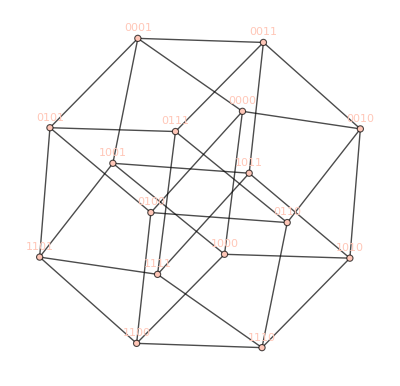

```mathematica
Table[HypercubeGraph[i,VertexSize->Small,EdgeStyle->{Black},VertexStyle->RGBColor[1,.78,.72],VertexLabels->Table[k->Placed[ If[StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]<i,Magnify[StringJoin[Table["0",i-StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]]]<>ToString[FromDigits[Flatten[IntegerDigits[{k-1},3]]]],3],Magnify[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]],3]],Above],{k,0,2^i}]],{i,1,4}]
Table[PlanarGraph[HypercubeGraph[i,VertexSize->Small,EdgeStyle->{Black},VertexStyle->RGBColor[1,.78,.72],VertexLabels->Table[k->Placed[ If[StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]<i,Magnify[StringJoin[Table["0",i-StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},3]]]]]]]<>ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]],3],Magnify[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]],3]],Above],{k,0,2^i}]]],{i,3,3}]
Table[HypercubeGraph[i,VertexSize->Small,EdgeStyle->{Black},VertexStyle->RGBColor[1,.78,.72],VertexLabels->Table[k->Placed[ If[StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]<i,Magnify[StringJoin[Table["0",i-StringLength[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]]]]]<>ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]],3],Magnify[ToString[FromDigits[Flatten[IntegerDigits[{k-1},2]]]],3]],Above],{k,0,2^i}]],{i,4,4}]
```

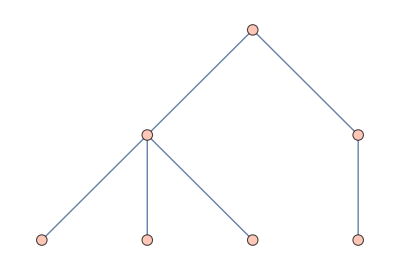

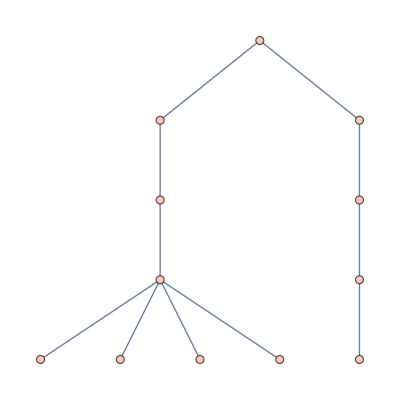

```mathematica
(*Table[TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,4+i],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]],{i,1,6}]*)
TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,5],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,10],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,20],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,30],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
```

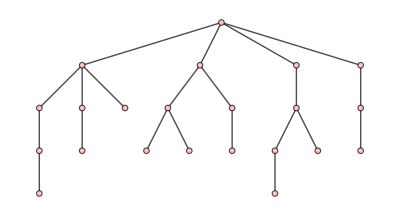

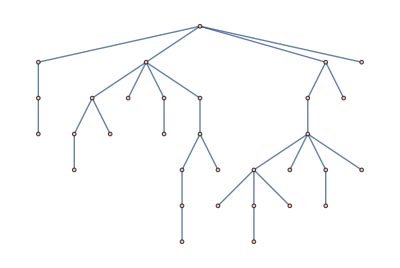

```mathematica
TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,30],VertexStyle->RGBColor[1,.78,.72],GraphLayout->"SpringElectricalEmbedding"]
```

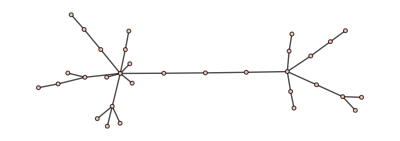

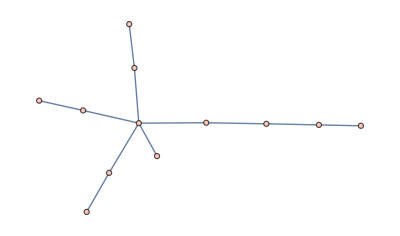

```mathematica
TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0,10],VertexStyle->RGBColor[1,.78,.72],GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
ConnectedGraphQ[-Graphics-]
g=AdjacencyGraph[Normal[AdjacencyMatrix[-Graphics-]],VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->Table[k-> Magnify[ToString[k],3],{k,1,8}]]
FindSpanningTree[g,Method->"Kruskal"];
HighlightGraph[g,%,GraphHighlightStyle->"Thick"]
```

True

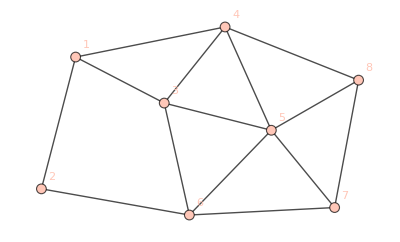

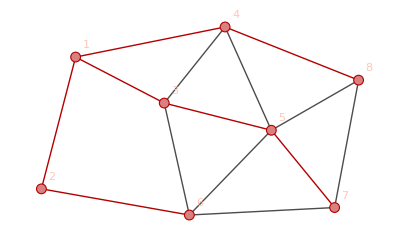

```mathematica
Table[CirculantGraph[10,i,PlotLabel->Subscript[C, 10,i] ,VertexStyle->RGBColor[1,.78,.72]],{i,1,5}]
```